```mathematica
$Assumptions=ϵ ∈ Reals && ϵ1 ∈ Reals && ϕ ∈ Reals && γl∈ Reals && γr∈ Reals && t0 ∈ Reals
Assumptions->$Assumptions
```

ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

Assumptions→ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

```mathematica
n=20;
l=2;
r=5; 

MZero=ConstantArray[0,{n,n}];

Id =IdentityMatrix[n];
ME= ϵ Id //Simplify;

(*constructing the T and H matrices*)
MT=MZero;
For[i=1, i<n+1, i++, MT[[Mod[i,n]+1,i]]=t];
For[i=1, i<n+1, i++, MT[[i, Mod[i,n]+1]]=ts];

MH= ϵ1 Id + MT;

(*constructing the Gamma matrices*)
MΓL= MZero;
MΓL[[l,l]]=γl;

MΓR= MZero;
MΓR[[r,r]]=γr;

MΓ= MΓL + MΓR;



(*check by printing*)
(*MH= ϵ1 Id + MT //MatrixForm
MΓL //MatrixForm
MΓR //MatrixForm
MΓ //MatrixForm*)
```

```mathematica
t=E^(I ϕ) t0;
ts= E^ (-I ϕ) t0;


MGr = ME - MH  + I MΓ/2;
MGa = ME - MH  - I MΓ/2;

(* to see the matrices
*)
(*ME - MH  + I MΓ/2//MatrixForm
ME - MH  - I MΓ/2//MatrixForm*)



Clear[ ϵ1, γl, γr, t0, ϕ]
ϵ1=0;
γl=0.1;
γr=0.5;
t0=1;
ϕ=2 Pi/5;



fGr[ϵ_]=Inverse[MGr];
fGa[ϵ_]=Inverse[MGa];


PlotStyle->{Thick,Automatic,Red,Dashed}


transmission[e_]=γl γr fGr[e][[r,l]]  fGa[e][[l,r]];
```

Inverse::sing: Matrix … is singular.

Part::partw: Part 5 of … does not exist.

Inverse::sing: Matrix … is singular.

Part::partw: Part 2 of … does not exist.

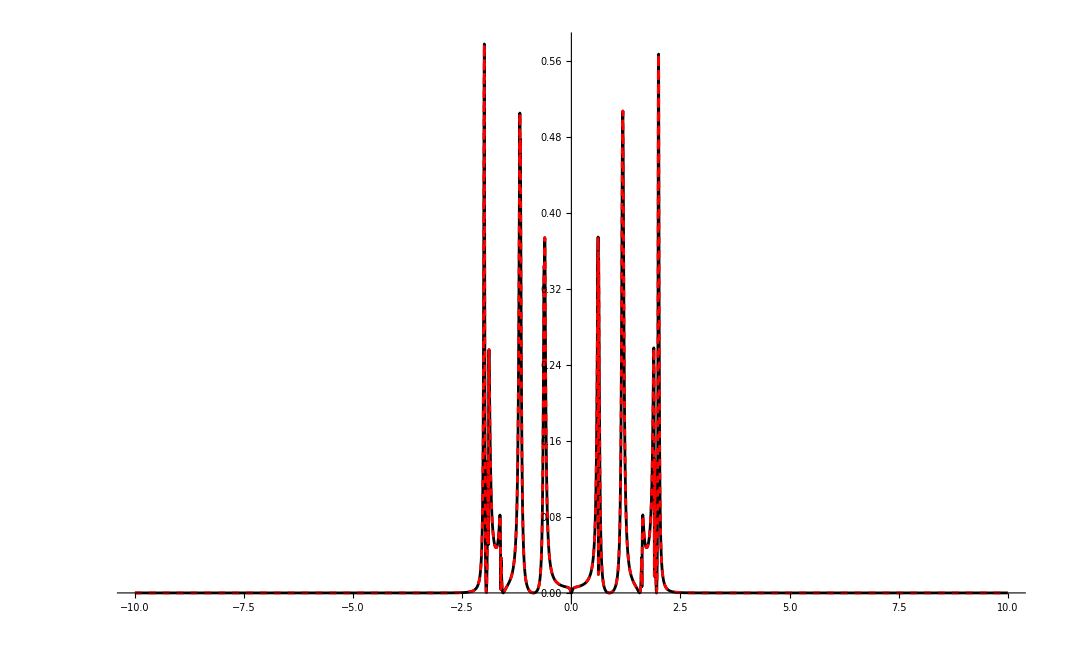

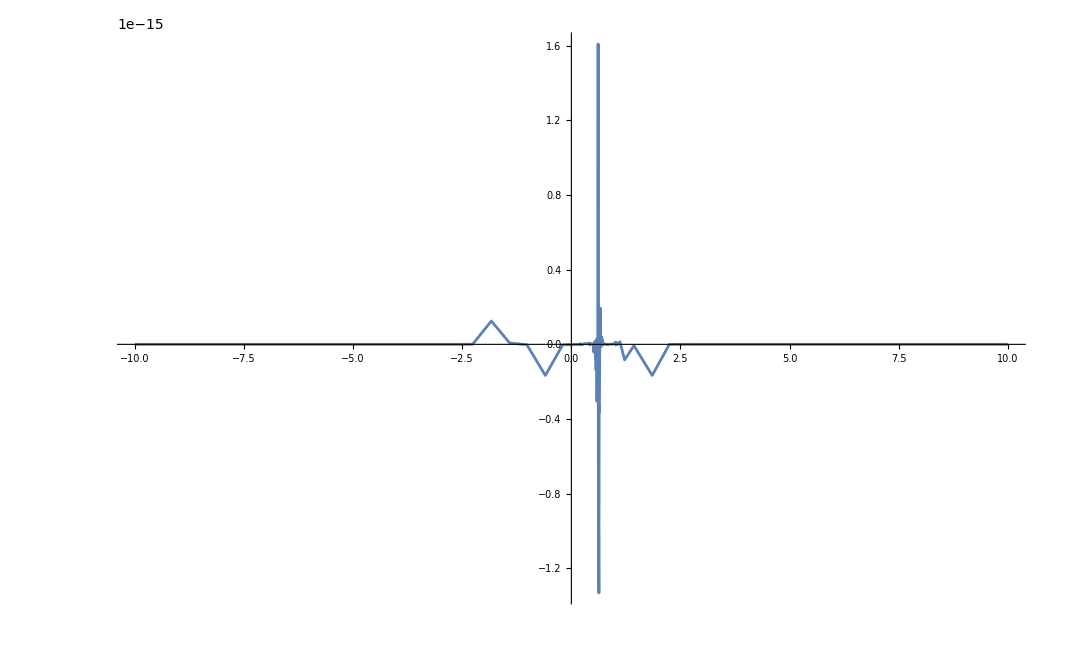

```mathematica
Plot[{Re@transmission[e], Re@transmission[-e]}, {e, -10. ,10. }, PlotRange->All,PlotStyle->{Black,{Red,Dashed}} ]
Plot[Re@transmission[e]-Re@transmission[-e], {e, -10. ,10. }, PlotRange->All]
```